# ΛCDM Cosmological Model

## Calculations for problem 7

### Inputing the parameters of the model

```mathematica
h=.7;

dH=3000*h^-1;
tH=9.78*h^-1*10^9;

ΩM=.3;
ΩR=2.8*10^-4;

Eh=Function[{a},Sqrt[ΩM*a^-3+ΩR*a^-4+(1-ΩM-ΩR)]];
```

### Plotting the Lookback Time and Computing the Age of the Universe (a)

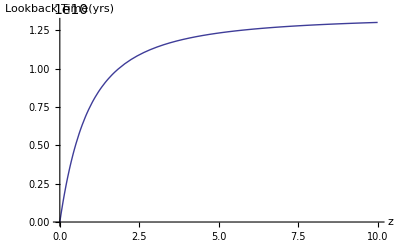

```mathematica
Clear[z,zmax]
zmax = 10;
Plot[tH*NIntegrate[1/((1+z)*Eh[1/(1+z)]),{z,0,z0}],{z0,0,zmax},PlotRange->Full,AxesLabel->{"z","Lookback Time(yrs)"}]
```

```mathematica
z=1;
tH*NIntegrate[1/((1+x)*Eh[1/(1+x)]),{x,z,∞}]
```

5.75287×10^9

For z = 1100 we find the age of the Universe to be 270369(465487) years old.
For z = 10 we find the age of the Universe to be 4.59725×10^8(4.65986×10^8) years old.
For z =1 we find the age of the Universe to be 5.73795×10^9(5.75287×10^9) years old.

### Plotting the Comoving Radial Distance and distance travelled by Relativistic Particles (b)

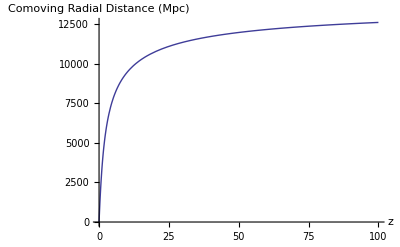

```mathematica
Clear[z,zmax]
zmax = 10;
Plot[dH*NIntegrate[1/Eh[1/(1+x)],{x,0,z}],{z,0,100},PlotRange->Full,AxesLabel->{"z","Comoving Radial Distance (Mpc)"}]
```

```mathematica
z=.2;
dH*NIntegrate[1/Eh[1/(1+x)],{x,0,z}]
```

817.24

Photons emitted at z = 1100  have travelled 13693 Mpc (44.7 Gltyrs)
Neutrinoes emitted at z = 10^10 have travelled 14164.5 Mpc (46.2 Gltyrs)

### Angular and Luminosity Distance Calulations (c)

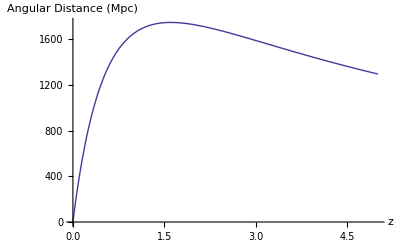

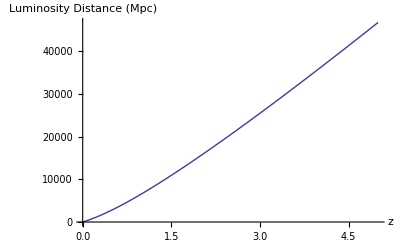

```mathematica
Clear[z,zmax]
zmax = 5;
Plot[(1+z)^-1*dH*NIntegrate[1/Eh[1/(1+x)],{x,0,z}],{z,0,zmax},PlotRange->Full,AxesLabel->{"z","Angular Distance (Mpc)"}]
Plot[(1+z)*dH*NIntegrate[1/Eh[1/(1+x)],{x,0,z}],{z,0,zmax},PlotRange->Full,AxesLabel->{"z","Luminosity Distance (Mpc)"}]
```

```mathematica
z=10^10;
{(1+z)^-1,1+z}*dH*NIntegrate[1/Eh[1/(1+x)],{x,0,z}]
```

{1.41645×10^-6,1.41645×10^14}

For z = 1100 the angular and luminosity distances are, respectively 12.4369Mpc and 1.5076×10^7 Mpc
For z = 10^10 they are 1.41645pc and 1.41645×10^14 Mpc 

The angular distance is the distance in Euclidean space that an object of known size would have to be to appear its given angular size. Since the Angular distance function has a maximum around two, it means that if you moved an object past that redshift, it would start to look larger even though it’s farther away. This is because due to the expansion of space, an object of given size would occupy more space in the early universe and hence appear larger than it should be.

The luminosity distance is the distance in Euclidean space that an object of of known luminosity would have to be in order to appear it’s given luminosity. Due to the expansion of space, the apparent luminosity of an object is less than it should be, hence the luminosity distance is larger than the actual distance to the object.

### Communicating with Galaxies

```mathematica
z=2;
tH*NIntegrate[1/((1+x)*Eh[1/(1+x)]),{x,0,z}]
```

1.02425×10^10

A galaxy at z = 1 is currently 3.31 Gpc from the Milky Way. A galaxy at z = 2 is at 5.18 Gpc.

If we attempted to send a signal to the first Galaxy it would take 7.71698×10^9 years to reach it. To the farther galaxy it would take 1.02425×10^10years.